## Construct the mask

```mathematica
(* construct recursively a mask matrix *)
recur[{m1_,m2_,m3_,n2_}]:=Block[{m},
(* create the new m2 array *)
m=ConstantArray[0,{Fibonacci[n2+2],Fibonacci[n2+2]}];

(* fill the 4 molecular clusters *)
m[[1;;Fibonacci[n2],1;;Fibonacci[n2]]]=m2;
m[[1;;Fibonacci[n2],Fibonacci[n2+1]+1;;Fibonacci[n2+2]]]=m2;
m[[Fibonacci[n2+1]+1;;Fibonacci[n2+2],1;;Fibonacci[n2]]]=m2;
m[[Fibonacci[n2+1]+1;;Fibonacci[n2+2],Fibonacci[n2+1]+1;;Fibonacci[n2+2]]]=m2;

(* fill the atomic cluster *)
m[[Fibonacci[n2]+1;;Fibonacci[n2+1],Fibonacci[n2]+1;;Fibonacci[n2+1]]]=m3;

{m,m1,m2,n2+1}]
```

```mathematica
m10={{1,1,0,1,1},{1,1,0,1,1},{0,0,1,0,0},{1,1,0,1,1},{1,1,0,1,1}};
m20={{1,0,1},{0,1,0},{1,0,1}};
m30={{1,1},{1,1}};
n0=4;
```

```mathematica
Nest[recur,{m10,m20,m30,n0},10][[1]]//MatrixPlot
```

-Graphics-

## Intensitites

### Geometrical construction

```mathematica
(* construct recursively the matrix of intensities *)
recInt[{m1_,m2_,m3_,n2_}]:=Block[{m},
(* create the new m2 array *)
m=ConstantArray[0,{Fibonacci[n2+2],Fibonacci[n2+2]}];

(* fill the 4 molecular clusters *)
m[[1;;Fibonacci[n2],1;;Fibonacci[n2]]]=m2/2;
m[[1;;Fibonacci[n2],Fibonacci[n2+1]+1;;Fibonacci[n2+2]]]=m2/2;
m[[Fibonacci[n2+1]+1;;Fibonacci[n2+2],1;;Fibonacci[n2]]]=m2/2;
m[[Fibonacci[n2+1]+1;;Fibonacci[n2+2],Fibonacci[n2+1]+1;;Fibonacci[n2+2]]]=m2/2;

(* fill the atomic cluster *)
m[[Fibonacci[n2]+1;;Fibonacci[n2+1],Fibonacci[n2]+1;;Fibonacci[n2+1]]]=m3;

{m,m1,m2,n2+1}]
```

```mathematica
i10={{1/4,1/4,0,1/4,1/4},{1/4,1/4,0,1/4,1/4},{0,0,1,0,0},{1/4,1/4,0,1/4,1/4},{1/4,1/4,0,1/4,1/4}};
i20={{1/2,0,1/2},{0,1,0},{1/2,0,1/2}};
i30={{1/2,1/2},{1/2,1/2}};
n0=4;
```

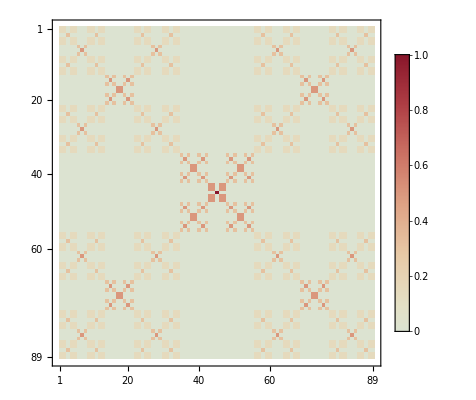

```mathematica
int=Nest[recInt,{i10,i20,i30,n0},6][[1]];
MatrixPlot[int,ColorFunction->"ThermometerColors",PlotLegends->Automatic]
```

### Comparison with numerics

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* wavefunctions in the co-basis, ordered by IDoS label *)
wf=Block[{val,vec,i=9,ts=10.,tw=1.},
{val,vec}=Eigensystem[hp[i,tw,ts]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
```

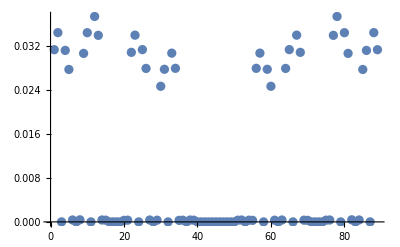

```mathematica
a=60;
ListPlot[{(Abs[wf]^2)[[a]]},PlotRange->All]
```

### Guessing fractal dimensions

#### Numerics

```mathematica
(* wf is a list of numbers that are a priori the coefficients of a wavefunction. They can be coefficients in the position basis, for a given energy, or coefficients in the energy basis for a particular position. *)
WfD[wf_,q_]:=-(q-1)^-1 Log[Plus@@(Abs[wf]^(2q))]/Log[Length@wf]
```

```mathematica
(* take a renormalization path (seq), a site label (i) and an approximant size (n) and return the new renormalization path, the new site label and the new size after one renormalization group operation *)
ClearAll[i];
iterSeq[{seq_,i_,n_}]:=Block[{inew=i,seqn=seq,nnew=n},
If[i>Fibonacci[n-1],seqn="m"<>seq;inew=i-Fibonacci[n-1];nnew=n-2;,
If[i>Fibonacci[n-2],seqn="a"<>seq;inew=i-Fibonacci[n-2];nnew=n-3,
seqn="m"<>seq;nnew=n-2;]];
{seqn,inew,nnew}
]

(* false when n<3 *)
test=#[[3]]≥3&;
(* take a site (i), a size (n) and return the renormalization path for this site *)
path[i_,n_]:=NestWhile[iterSeq,{"",i,n},test][[1]]->i
(* compute the relative time spent on molecular sites (x) *)
xPath[i_,n_]:={i,StringCount[NestWhile[iterSeq,{"",i,n},test][[1]],"m"]/n}
(* generate the whole (x) tree! *)
tree[n_]:=xPath[#,n]&/@ Range[Fibonacci[n]]
```

```mathematica
ClearAll[ρ,q,val,vec,DxList,xlist,xvalues,listPos,avDx,tol];
avDx[ρ_,q_,n_]:=Block[{val,vec,DxList,xlist,xvalues,listPos,avDx,tol=10^-14},
(* compute wavefunctions and energies *)
{val,vec}=Eigensystem[hp[n,ρ,1.]];
(*order wavefunctions by increasing energy*)
vec=vec[[Ordering[val]]];
(* drop small components *)
vec=Chop[vec,tol];
(* list fractal dimensions, indexed by site *)
DxList=WfD[#,q]&/@Transpose[vec];

(* compute x for each site *)
xlist=tree[n+2];
(* drop the site labels, they are unecessary as x is indexed by increasing x label *)
xlist=Last@(Transpose[xlist]);

(* list all possible values of x *)
xvalues=Sort@DeleteDuplicates[xlist];
(* list all positions by increasing value of x *)
listPos=Flatten[Position[xlist,#]]&/@xvalues;
(* for each value of x compute the average - on positions corresponding to this x - fractal dimension *)
avDx=Mean[DxList[[#]]]&/@listPos;
(* return the average fractal dimension as a function of x *)
avDx=MapThread[{#1,#2}&,{xvalues,avDx}]
]
```

```mathematica
n=14;
q=10;
ρ=0.05;
lbl={"x","D^x(q="<>ToString[q]<>",ρ="<>ToString[ρ]<>")"};
avd=avDx[ρ,q,n];
```

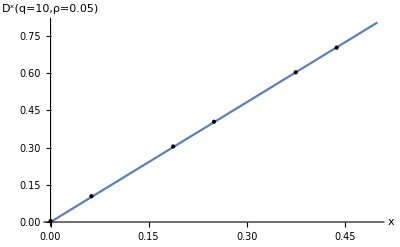

```mathematica
Plot[x ((n+2)Log[2])/Log[Fibonacci[n+2]],{x,0,1/2},Epilog->{PointSize[Medium],Point@dat},AxesLabel->lbl]
```

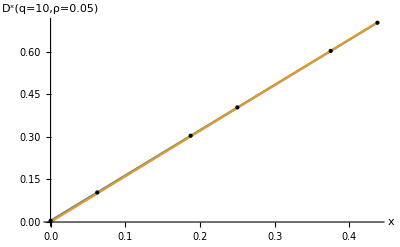

```mathematica
dat=avd;
m=Min[Transpose[avd][[1]]];
mm=Max[Transpose[avd][[1]]];
fit=LinearModelFit[dat,x,x];
Plot[{Normal[fit],x ((n+2)Log[2])/Log[Fibonacci[n+2]]},{x,m,mm},Epilog->{PointSize[Medium],Point@dat},AxesLabel->lbl]
```

#### Geometrical

```mathematica
n=17;
int=Nest[recInt,{N[i10],i20,i30,n0},n-3][[1]];
DxList=WfD[#,q]&/@Transpose[√int];
```

(D^n)_q(x) is exactly x (Log(2))/(Log(F_n^(1/n))), and Log(F_n^(1/n)) converges slowly to Log(τ).

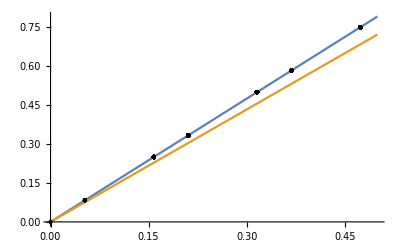

```mathematica
pts=MapThread[{#1,#2}&,{Last[Transpose[tree[n+2]]],DxList}];
Plot[{x ((n+2)Log[2])/Log[Fibonacci[n+2]],x Log[2]/Log[GoldenRatio]},{x,0,1/2},Epilog->{PointSize[Medium],Point@pts}]
```